```mathematica
Table[1/n//RealDigits//First//Flatten//Length,{n,2,200}]
```

{1,1,2,1,2,6,3,1,1,2,2,6,6,1,3,16,1,18,1,6,2,22,3,1,6,3,7,28,1,15,4,2,16,6,2,3,18,6,2,5,6,21,3,1,22,46,4,42,1,16,7,13,3,2,8,18,28,58,2,60,15,6,5,6,2,33,17,22,6,35,3,8,3,2,19,6,6,13,3,9,5,41,7,16,21,28,4,44,1,6,23,15,46,18,5,96,42,2,1,4,16,34,7,6,13,53,3,108,2,3,8,112,18,22,28,6,58,48,2,22,60,5,15,1,6,42,5,21,6,130,2,18,33,3,17,8,22,46,6,46,35,6,3,28,8,42,3,148,1,75,19,16,6,15,6,78,13,13,3,66,9,81,5,2,41,166,7,78,16,18,21,43,28,6,4,58,44,178,1,180,6,60,23,3,15,16,46,6,18,95,5,192,96,6,42,98,2,99,1}

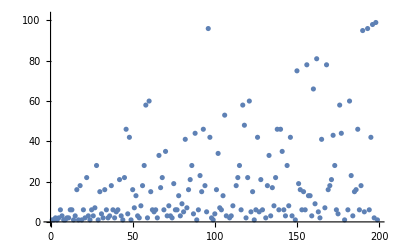

```mathematica
ListPlot[%174]
```

```mathematica
Table[(m/n)//RealDigits//First//Flatten//Length,{n,2,100},{m,2,100}]//ArrayPlot
```

-Graphics-